```mathematica
ClearAll["Global`*"]
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/carnivoredensities_trimmed.csv"}],"csv"];
ppmrfitdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/ppmr_fit_table_revreps.csv"}],"csv"];
```

```mathematica
ppmrfitdata
```

{{Fit,FitLow,FitHigh},{3.62176,3.59524,3.64827},{0.225214,0.220901,0.229527}}

```mathematica
ppmrfitdata[[2,1]]
ppmrfitdata[[3,1]]
```

3.62176

0.225214

```mathematica
eqnC = λ*(R/(k/2+R))*C-( σ*(1-R/k)+μ+((1+mod)*bP))*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],ρ->ρ[M],σ->σ[M],bP->bP[M]};(*take σ*(1-R/k)=0 to take out starvation component*)
eqnR = α*R*(1-R/(k))-( λ/Y*(R/(k/2+R))+ρ)*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],ρ->ρ[M],σ->σ[M],bP->bP[M]};
LVSS = FullSimplify[Solve[{0==eqnC,0==eqnR},{C,R}]];
Csol = C/.LVSS[[3]]
Rsol = R/.LVSS[[3]]
```

-((α Y[M] (4 kRes (1+mod)^3 bP[M]^3-2 λ[M] μ[M] √(kRes^2 (4 ((1+mod) bP[M]-λ[M]+μ[M])^2+4 (3 (1+mod) bP[M]-λ[M]+3 μ[M]) σ[M]+9 σ[M]^2))+2 μ[M]^2 √(kRes^2 (4 ((1+mod) bP[M]-λ[M]+μ[M])^2+4 (3 (1+mod) bP[M]-λ[M]+3 μ[M]) σ[M]+9 σ[M]^2))-2 Y[M] λ[M] ρ[M] √(kRes^2 (4 ((1+mod) bP[M]-λ[M]+μ[M])^2+4 (3 (1+mod) bP[M]-λ[M]+3 μ[M]) σ[M]+9 σ[M]^2))+2 Y[M] μ[M] ρ[M] √(kRes^2 (4 ((1+mod) bP[M]-λ[M]+μ[M])^2+4 (3 (1+mod) bP[M]-λ[M]+3 μ[M]) σ[M]+9 σ[M]^2))-2 λ[M] σ[M] √(kRes^2 (4 ((1+mod) bP[M]-λ[M]+μ[M])^2+4 (3 (1+mod) bP[M]-λ[M]+3 μ[M]) σ[M]+9 σ[M]^2))+2 μ[M] σ[M] √(kRes^2 (4 ((1+mod) bP[M]-λ[M]+μ[M])^2+4 (3 (1+mod) bP[M]-λ[M]+3 μ[M]) σ[M]+9 σ[M]^2))-Y[M] ρ[M] σ[M] √(kRes^2 (4 ((1+mod) bP[M]-λ[M]+μ[M])^2+4 (3 (1+mod) bP[M]-λ[M]+3 μ[M]) σ[M]+9 σ[M]^2))+kRes (4 (λ[M]-μ[M])^2 (μ[M]+Y[M] ρ[M])+2 (2 λ[M]^2-5 λ[M] μ[M]+μ[M] (5 μ[M]+2 Y[M] ρ[M])) σ[M]+(-2 λ[M]+6 μ[M]+3 Y[M] ρ[M]) σ[M]^2)+2 (1+mod)^2 bP[M]^2 (kRes (-4 λ[M]+6 μ[M]+2 Y[M] ρ[M]+5 σ[M])+√(kRes^2 (4 ((1+mod) bP[M]-λ[M]+μ[M])^2+4 (3 (1+mod) bP[M]-λ[M]+3 μ[M]) σ[M]+9 σ[M]^2)))-2 (1+mod) bP[M] (kRes (-2 (λ[M]-μ[M]) (λ[M]-3 μ[M]-2 Y[M] ρ[M])+(5 λ[M]-2 (5 μ[M]+Y[M] ρ[M])) σ[M]-3 σ[M]^2)+λ[M] √(kRes^2 (4 ((1+mod) bP[M]-λ[M]+μ[M])^2+4 (3 (1+mod) bP[M]-λ[M]+3 μ[M]) σ[M]+9 σ[M]^2))-2 μ[M] √(kRes^2 (4 ((1+mod) bP[M]-λ[M]+μ[M])^2+4 (3 (1+mod) bP[M]-λ[M]+3 μ[M]) σ[M]+9 σ[M]^2))-Y[M] ρ[M] √(kRes^2 (4 ((1+mod) bP[M]-λ[M]+μ[M])^2+4 (3 (1+mod) bP[M]-λ[M]+3 μ[M]) σ[M]+9 σ[M]^2))-σ[M] √(kRes^2 (4 ((1+mod) bP[M]-λ[M]+μ[M])^2+4 (3 (1+mod) bP[M]-λ[M]+3 μ[M]) σ[M]+9 σ[M]^2)))))/(4 σ[M]^2 (2 (λ[M]+Y[M] ρ[M]) ((1+mod) bP[M]+μ[M]+Y[M] ρ[M])+(2 λ[M]+3 Y[M] ρ[M]) σ[M])))

(kRes (2 (1+mod) bP[M]-2 λ[M]+2 μ[M]+σ[M])+√(kRes^2 (8 σ[M] ((1+mod) bP[M]+μ[M]+σ[M])+(2 (1+mod) bP[M]-2 λ[M]+2 μ[M]+σ[M])^2)))/(4 σ[M])

Metabolic parameters for herbivore consumer

```mathematica
kRes=23000;(*grams/m^2 carrying capacity of resource*)

Ed=18200; (*J/g of plant Resource *)
B0=4.7*10^(-2);(*W g^−0.75 for herbivores*)
Em=5774;(*J/gram - energy required to build gram of herbivore*)
a = B0/Em;

(*s=1;*)
Emprime =7000;
aprime =  B0/Emprime;
γ=1.19;
ζ=1.00;
f0=0.0202;
mm0=0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9));


τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate of herbivore *)
BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
m0[M_]:=0.097*M^0.92;

(*k=(*10*)23000/2;*)
ρ[M_]:=B0*M^(η)/(M*Ed);
a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
μ[M_] := (a0*(Exp[a1*a2*M^(b1+b2)]-1)*M^(b0-b1-b2))/(a1*a2)   (* this is the consumer death rate*)
(*STARVATION MORTALITY*)
ϵsig[M_] := (1-(f0*M^γ+mm0*M^ζ)/M);(*mortality from starvation state*)
τsig [M_]:=-M^(1/4)/aprime*Log[ϵsig[M]];(*time it takes to go from full to dead*)
σ[M_] := 1/τsig [M];(*starvation mortality rate)*)
```

Metabolic parameters for predator that eats herbivore consumer

```mathematica
η=3/4;
(*B0=4.7*10^(-2);(*W g^−0.75*)*)
B0Pred =(10^0.32)(*kJ/day*)*((0.01157(*Watts*))/(1(*kJ/day*))); (* in (kJ/d) for carnivora from https://doi.org/10.1086/432852 USING LOG10!!!!! *)
EmPred=5774;(*Energy to synthesize a unit of biomass not during starvation J/gram*)

aPred = B0Pred/EmPred;
m0Pred[Mp_]:=0.097*Mp^0.92;
ϵLam = 0.95;
τLamPred[Mp_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0Pred[Mp]/Mp)^(1/4))]*(4*Mp^(1/4))/aPred;
λPred[Mp_]:=(Log[2]/τLamPred[Mp]) (*Fecundity = 2*) 
Bpred[Mp_]:=Integrate[(((1-(1-(m0Pred[Mp]/Mp)^(1/4))*E^(-aPred*t/(4*Mp^(1/4)))))^4)*Mp,{t,0,τLamPred[Mp]}]
```

Predator/prey interaction parameters

```mathematica
PredsperArea[Mp_] :=(0.000862119)*Mp^-0.88; (*Inds/m^2 w/ Mp (grams) From Carbone and Gittleman, Science 2002*)
PredDensity[Mp_] := Mp*PredsperArea[Mp]; (*grams/ind * inds/meter^2 = grams/m^2*)
(*Parameterizations of the Rohr Model*)

(*palpha = 1.6332;
pbeta = 0.2109;
pgamma = -0.3731;*)
(*p = Exp[linkalpha + linkbeta*Log[M/Mp] + linkgamma*Log[M/Mp]^2];
prob = p/(1+p);
OptMass =M/.Solve[ D[prob,M]==0,M][[1]];*)

(*OptPreyMass[Mp_] :=ⅇ^(-pbeta/(2 pgamma)) Mp;*)
(*OptPreyMass[Mp_]:=ⅇ^(pbeta/(2 pgamma)) *Mp;*)

(*OptPredMass[M_]:=ⅇ^(pbeta/(2 pgamma)) M;*)
(*OptPredMass[M_]:=ⅇ^(-pbeta/(2 pgamma)) *M;*)



(*--------------------*)
(*Optimal Predator mass given Prey (M) Mass*)
OptPredMass[M_]:=(1+κint)*ppmrint*M^(ppmrslope*(1+κslope));
ppmrslope = (ppmrfitdata[[3,1]]);
ppmrint = Exp[(ppmrfitdata[[2,1]])]*((1/1000)^ppmrslope)*1000; (*converted from KG to grams*)

(*Inverse: Optimal Prey mass given Predator (Mp) Mass*)
OptPreyMass[Mp_]:=Evaluate[M/.Solve[OptPredMass[M]==Mp,M][[1]]];

(*--------------------*)



OptPreypermeter2[Mp_] := 0.1156*OptPreyMass[Mp]^-0.77;
(*Damuth: Average Individuals/m2*)
OptPreygramspermeter2[Mp_] :=OptPreypermeter2[Mp]*OptPreyMass[Mp] ;
(*Average Individuals/m2 * average grams/individual*)
(*Percent fat + muscle*)
(*percentconsumable[M_]:=( 0.02*M^1.19 + 0.38*M^1.00)/M;*)
(*Or 1 - percent skeletal*)
massSkeletalgrams[M_]:= 0.0335*M^1.09263;
massFatgrams[M_]:=0.02*M^1.19;
massMusclegrams[M_]:=0.38*M^1.0;
massOthergrams[M_]:=M-(massSkeletalgrams[M]+massFatgrams[M]+massMusclegrams[M]);
(*This is nearly 100% from Prange et al. AmNat 1979*)
(*Energy Density of PREY Joules/gram*)
(*BLUBBER energy content 37670 J/gram SAME AS FAT *)
(*NOTE: THINK CAREFULLY ABOUT THIS *)
FatJperG = 37700;
ProteinJperG = 17900;
MuscleJperG = 0.4*ProteinJperG + 0.6*FatJperG;
(*TissueJperG = ProteinJperG+FatJperG;
PercentFat =(FatJperG/TissueJperG);
PercentProtein =(1- PercentFat);*)
Eprey[M_]:=(1/(M))*(massFatgrams[M]*FatJperG+massMusclegrams[M]*MuscleJperG+massOthergrams[M]*MuscleJperG);
(*Eprey[M_,ϵEprey_] := ((PercentProtein*TissueJperG)+(PercentFat*TissueJperG)+0)*(1+ϵEprey)*percentconsumable[M];*)
(*Joules/gram: 17000 protein + 37000 fat + 0 carb per gram of meat http://www.fao.org/3/y5022e/y5022e04.htm  Modified from Merrill and Watt (1973).*)
(*Results of MAXSIZE are very sensitive to Energy Density of Prey*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Calculate Herbivore Yield

```mathematica
YHerbperRes[M_]:=M*Ed/BLam[M]; (*Grams herb / Grams Resource given the mass of an Herbivore*)
Y[M_]:=YHerbperRes[M];
(*kprey[Mp_]:=OptPreygramspermeter2[Mp]; *)(*PREY carrying capacity grams/m^2*)
```

Check Original Model w/o predation... do we get pretty close to the Damuth Data without predation?

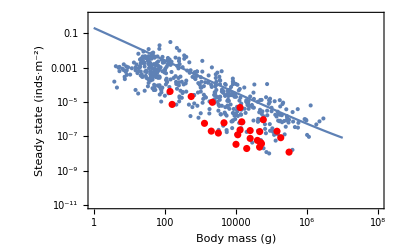

```mathematica
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5}],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[((1/M)*Csol/.{mod->0,bP[M]->0,κint->0,κslope->0}),{M,1,10^7},Frame->True,PlotStyle->ColorData[97,1]]
}]
```

Calculate Predator Yield

```mathematica
(*Yield of predator per prey*)
Ypred[Mp_,M_] := (Mp*Eprey[M])/Bpred[Mp]; (*Grams of predator per grams of prey*)
```

Calculate Consumer and Predator Boundary Densities

```mathematica
PreyDensityTheoreticalMax[M_] :=  Evaluate[YHerbperRes[M]*kRes//Simplify]; (*Grams Herb / m^2 given the mass of a predator and the optimal prey mass given predator mass conversion*)
PreyDensityTheoreticalHalfSat[M_]:=(PreyDensityTheoreticalMax[M]*(1-χ))/χ/.χ->0.99;
PredatorDensityTheoreticalMax[Mp_,M_]:= Evaluate[Ypred[Mp,M]*YHerbperRes[M]*kRes//Simplify];
```

Two Predator reproduction rates : linear to the theoretical maximum and M-M with saturation derived from the theoretical maximum

```mathematica
Plot[{λPred[OptPredMass[M]]*ConsumerDensity/PreyDensityTheoreticalMax[M],λPred[OptPredMass[M]]*(ConsumerDensity/(PreyDensityTheoreticalHalfSat[M]+ConsumerDensity))},{ConsumerDensity,0,PreyDensityTheoreticalMax[M]}]/.M->10^7
```

Plot::plln: Limiting value (3.87851×10^11 M^(3/4))/((1/(1-0.558075/M^(«20»)))^4. (0.291 (-1+(3.79423×10^7)/Power[«2»]^4.) M^0.92+(«11»+6.69691/M^(«20»)) M-(4.55308×10^8 M Log[0.0127415/Plus[«2»]])/(1/(1+Times[«1»]))^4.)) in {ConsumerDensity,0,(3.87851×10^11 M^(3/4))/((1/(1-0.558075/M^(«20»)))^4. (0.291 (-1+3.79423×10^7 Power[«2»]) M^0.92+(«11»+6.69691 Power[«2»]) M-(4.55308×10^8 M Log[0.0127415 Power[«2»]])/(1/Plus[«2»])^4.))} is not a machine-sized real number.

-Graphics-

Plot the Theoretical Maxima for herbivore consumers and predators relative to Damuth Data

```mathematica
(*Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_maxdensities.pdf"}],PredPlot,"PDF"]*)
```

Calculate per-capita Predation Mortality Rate as (predation rate per gram consumer)*(predated consumer density)

```mathematica
predgrowthrateperconsumer[Mp_,M_] :=λPred[Mp]/PreyDensityTheoreticalMax[M];
predatedconsumerdensity[Mp_,M_]:=PredDensity[Mp]/Ypred[Mp,M];
(*predrate[Mp_,M_,ϵEprey_] := (λPred[Mp]*PredDensity[Mp])/PredDensityMaxPreyGrowth[Mp,M,ϵEprey](*((1/time)*gpred/m^2)/(gpred/m^2)=1/time*);*)
predmortality = FullSimplify[predgrowthrateperconsumer[Mp,M]*predatedconsumerdensity[Mp,M]];
predmortalityfull[Mp_,M_]:=  Evaluate[predmortality//Simplify];

bP[M_] :=predmortalityfull[OptPredMass[M],M];
```

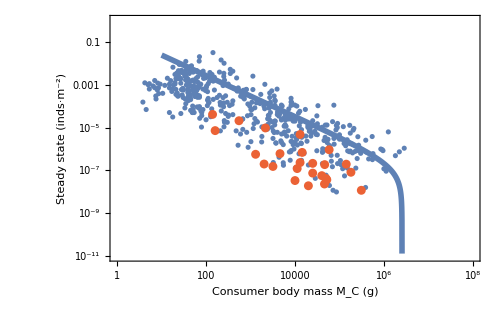

```mathematica
ConsInstabilityPlot = Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer body mass M_C (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->ColorData[97,4]],
LogLogPlot[(1/M)*Csol/.{mod->0,κint->0,κslope->0},{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],ColorData[97,1]}]
},ImageSize->500]
```

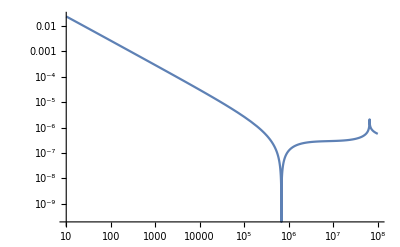

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

2.54916×10^6

7893.46 (2.54916×10^6)^(0.225214 (1+κslope)) (1+κint)

```mathematica
LogLogPlot[Abs[(1/M)*Csol/.{mod->1,κint->0,κslope->0}],{M,10,10^8}]
PreySSMin=N[(FindMinimum[Abs[(1/M)*Csol/.{mod->0,κint->0,κslope->0}],M])];
MaxPreyMassSS=M/.PreySSMin[[2]]
MaxPredMassSS = OptPredMass[MaxPreyMassSS]
```

```mathematica
MaxPreyMassSSVar1 = ParallelTable[Quiet[{(M/.(N[(FindMinimum[Abs[(1/M)*Csol/.{mod->i,κint->0,κslope->0}],M])])[[2]]),1+i}],{i,-0.1,0.1,0.01}];
MaxPreyMassSSVar2 = ParallelTable[Quiet[{(M/.(N[(FindMinimum[Abs[(1/M)*Csol/.{mod->i,κint->0,κslope->0}],M])])[[2]]),1+i}],{i,-0.99,1,0.01}];
```

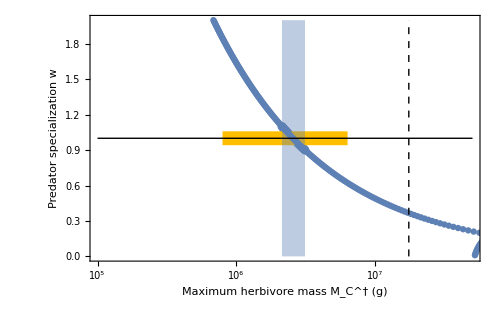

```mathematica
MaxPreyMassVarPlot= Show[{
ListLogLinearPlot[MaxPreyMassSSVar1,PlotRange->{{10^5,5*10^7},{1+-1,1+1}},Frame->True,FrameLabel->{"Maximum herbivore mass M_C^† (g)","Predator specialization w"},PlotStyle->ColorData[97,1],LabelStyle->Directive[FontSize->16]],
Graphics[{Thickness[0.02],ColorData[97,8],Line[{{Log@794000,0+1},{Log@6309000,0+1}}]}],
Graphics[{Thickness[0.0],ColorData[97,1],Opacity[0.4],Rectangle[{Log@First[MaxPreyMassSSVar1][[1]],-1+1},{Log@Last[MaxPreyMassSSVar1][[1]],1+1},RoundingRadius->0.01]}],
ListLogLinearPlot[MaxPreyMassSSVar2],
Graphics[{Black,Thick,Dashed,Line[{{Log@(1.74*10^7),-1+1},{Log@(1.74*10^7),1+1}}]}],
Graphics[{Black,Thin,Line[{{Log@(1*10^5),1},{Log@(5*10^7),1}}]}]
},ImageSize->500]
(*MaxPreyMassVarPlot2= Show[{
ListLogLinearPlot[MaxPreyMassSSVar,PlotRange->{{10^5,10^7},{-1,1}},Frame->True,FrameLabel->{"Maximum herbivore mass M_C^†","Prop. Δ predation mortality rate"},PlotStyle->Black,LabelStyle->Directive[FontSize->16]],
Graphics[{ColorData[97,1],Opacity[0.5],Rectangle[{Log@First[MaxPreyMassSSVar][[1]],-0.15},{Log@Last[MaxPreyMassSSVar][[1]],0.15}]}]
},ImageSize->500]*)
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_maxpreyvar.pdf"}],MaxPreyMassVarPlot,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2021_TaranWebs/figures/fig_maxpreyvar.pdf

```mathematica
First[MaxPreyMassSSVar2]
Last[MaxPreyMassSSVar2]
```

{5.20566×10^7,0.01}

{682933.,2.}

```mathematica
MaxObsPreySize = MaxPreyMassSSVar2[[Position[MaxPreyMassSSVar2[[All,1]],_?((#>1.70*10^7&&#<1.76*10^7)&)][[1]][[1]]]]
ModMaxObsPreySize = -(1-MaxObsPreySize[[2]]);
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/data_maxobspreysize_gen.csv"}],MaxObsPreySize,"CSV"];
```

{1.70864×10^7,0.37}

```mathematica
ModMaxObsPreySize
```

-0.63

```mathematica
1+ModMaxObsPreySize
```

0.37

```mathematica
MaxPreyMassSSVarSMALL = ParallelTable[Quiet[{(M/.(N[(FindMinimum[Abs[(1/M)*Csol/.{mod->i,κint->0,κslope->0}],M])])[[2]]),i}],{i,-0.99999,0.9,0.001}];
```

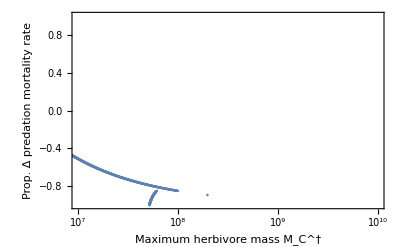

```mathematica
ListLogLinearPlot[MaxPreyMassSSVarSMALL,PlotRange->{{10^7,10^10},{-1,1}},Frame->True,FrameLabel->{"Maximum herbivore mass M_C^†","Prop. Δ predation mortality rate"},PlotStyle->ColorData[97,1],LabelStyle->Directive[FontSize->16]]
```

```mathematica
MaxPreyMassSSVarSMALL[[Position[MaxPreyMassSSVarSMALL[[All,1]],_?((#==Max[MaxPreyMassSSVarSMALL[[All,1]]])&)][[1]][[1]]]]
```

{1.07649×10^15,-0.87699}

```mathematica
First[MaxPreyMassSSVar1]
Last[MaxPreyMassSSVar1]
N[First[MaxPreyMassSSVar1][[1]]/MaxPreyMassSS]
N[Last[MaxPreyMassSSVar1][[1]]/MaxPreyMassSS]
```

{3.11597×10^6,0.9}

{2.12608×10^6,1.1}

1.22235

0.834032

```mathematica
ModMaxObsPreySize
```

-0.63

```mathematica
MaxConsumerSizePredPreyRatio=Flatten[ParallelTable[Quiet[{i,j,N[(M/.FindMinimum[Abs[(1/M)*Csol/.{mod->ModMaxObsPreySize,κint->i,κslope->j}],M][[2]])]}],{i,-0.99,2,0.01},{j,-0.99,2,0.01}],1];
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/data_maxconsumersizepredpreyratio_gen.csv"}],MaxConsumerSizePredPreyRatio,"CSV"];
```

```mathematica
(*MaxConsumerSizePredPreyRatio=Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/data_maxconsumersizepredpreyratio.csv"}]];
MaxConsumerSizePredPreyRatioSmall = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/data_maxconsumersizepredpreyratiosmall.csv"}]];
MaxPredatorSizePredPreyRatio = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/data_maxpredatorsizepredpreyratio.csv"}]];
MaxPredatorSizePredPreyRatioSmall = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/data_maxpredatorsizepredpreyratiosmall.csv"}]];*)

(*MaxConsumerSizePredPreyRatio=Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/data_maxconsumersizepredpreyratio_gen.csv"}]];*)
MaxConsumerSizePredPreyRatioSmall=Flatten[ParallelTable[Quiet[{i,j,N[(M/.FindMinimum[Abs[(1/M)*Csol/.{mod->ModMaxObsPreySize,κint->i,κslope->j}],M][[2]])]}],{i,-0.99,2,0.1},{j,-0.99,2,0.1}],1];
MaxPredatorSizePredPreyRatio=Table[{MaxConsumerSizePredPreyRatio[[i,1]],MaxConsumerSizePredPreyRatio[[i,2]],OptPredMass[MaxConsumerSizePredPreyRatio[[i,3]]]/.{mod->ModMaxObsPreySize,κint->MaxConsumerSizePredPreyRatio[[i,1]],κslope->MaxConsumerSizePredPreyRatio[[i,2]]}},{i,1,Dimensions[MaxConsumerSizePredPreyRatio][[1]]}];
MaxPredatorSizePredPreyRatioSmall=Table[{MaxConsumerSizePredPreyRatioSmall[[i,1]],MaxConsumerSizePredPreyRatioSmall[[i,2]],OptPredMass[MaxConsumerSizePredPreyRatioSmall[[i,3]]]/.{mod->ModMaxObsPreySize,κint->MaxConsumerSizePredPreyRatioSmall[[i,1]],κslope->MaxConsumerSizePredPreyRatioSmall[[i,2]]}},{i,1,Dimensions[MaxConsumerSizePredPreyRatioSmall][[1]]}];
```

```mathematica
SizePlotPositions =Intersection[Flatten[Position[MaxConsumerSizePredPreyRatio[[All,3]],_?(Re[#]>5*10^5&&Re[#]<1.74*10^7&)]],Flatten[Position[MaxPredatorSizePredPreyRatio[[All,3]],_?(Re[#]>5*10^5&&Re[#]<1.2*10^6 &)]]];
```

```mathematica
MegaMammalPlotGen=GraphicsRow[{
Show[{
ListDensityPlot[MaxConsumerSizePredPreyRatioSmall,PlotLegends->BarLegend[Automatic,LegendLabel->"M_C^† (g)"],FrameLabel->{"Prop. change PPMR χ_int","Prop. change PPMR χ_slope"}(*,RegionFunction->Function[{x,y,z},z>1.5*10^6&&z<1.74*10^7]*),ColorFunction->ColorData["AtlanticColors"],LabelStyle->Directive[FontSize->16],ScalingFunctions->{"Linear","Linear","Log"}],
ListPlot[Transpose[{MaxConsumerSizePredPreyRatio[[SizePlotPositions,1]],MaxConsumerSizePredPreyRatio[[SizePlotPositions,2]]}],Frame->True,PlotRange->{{-1,2},{-1,2}},AspectRatio->1,PlotStyle->Directive[White,Opacity[0.8]]](*,
Graphics[{Gray,Line[{0,-1},{0,2}]}],
Graphics[{Gray,Line[{-1,0},{2,0}]}]*)
},ImageSize->350],
Show[{
ListDensityPlot[MaxPredatorSizePredPreyRatioSmall,PlotLegends->BarLegend[Automatic,LegendLabel->"M_P^†(g)"],FrameLabel->{"Prop. change PPMR χ_int","Prop. change PPMR χ_slope"}(*,RegionFunction->Function[{x,y,z},z>500000&&z<1.2*10^6]*),ColorFunction->ColorData["SiennaTones"],LabelStyle->Directive[FontSize->16],ScalingFunctions->{"Linear","Linear","Log"}],
ListPlot[Transpose[{MaxConsumerSizePredPreyRatio[[SizePlotPositions,1]],MaxConsumerSizePredPreyRatio[[SizePlotPositions,2]]}],Frame->True,PlotRange->{{-1,2},{-1,2}},AspectRatio->1,PlotStyle->Directive[White,Opacity[0.8]]](*,
Graphics[{Gray,Line[{0,-1},{0,2}]}],
Graphics[{Gray,Line[{-1,0},{2,0}]}]*)
},ImageSize->350]
},ImageSize->950,Spacings->Scaled[-0.05]]
```

-Graphics-

```mathematica
(*Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_megamammal_generalist.pdf"}],MegaMammalPlotGen,"PDF"]*)
```

/Users/jdyeakel/Dropbox/PostDoc/2021_TaranWebs/figures/fig_megamammal_generalist.pdf

```mathematica
OptPredMass[M]
```

11786.8 M^(0.194142 (1+κslope)) (1+κint)

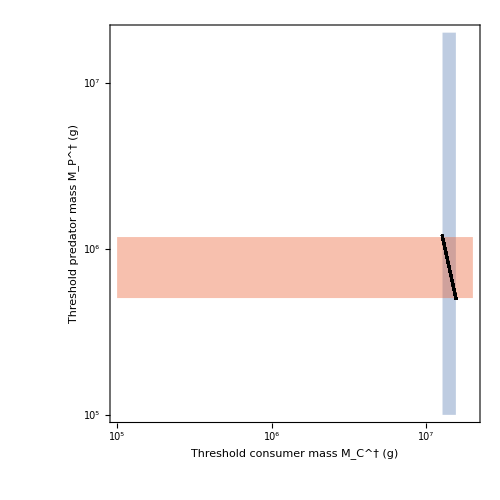

```mathematica
MegaMammalPlotGenSize=Show[{
ListLogLogPlot[Transpose[{MaxConsumerSizePredPreyRatio[[SizePlotPositions,3]],MaxPredatorSizePredPreyRatio[[SizePlotPositions,3]]}],PlotStyle->Black,Frame->True,PlotRange->{{1*10^5,2*10^7},{1*10^5,2*10^7}},FrameLabel->{"Threshold consumer mass M_C^† (g)","Threshold predator mass M_P^† (g)"},LabelStyle->Directive[FontSize->16]],
Graphics[{ColorData[97,1],Opacity[0.4],Rectangle[{Log@First[MaxConsumerSizePredPreyRatio[[SizePlotPositions,3]]],Log@(1*10^5)},{Log@Last[MaxConsumerSizePredPreyRatio[[SizePlotPositions,3]]],Log@(2*10^7)}]}],
Graphics[{ColorData[97,4],Opacity[0.4],Rectangle[{Log@(1*10^5),Log@First[MaxPredatorSizePredPreyRatio[[SizePlotPositions,3]]]},{Log@(2*10^7),Log@Last[MaxPredatorSizePredPreyRatio[[SizePlotPositions,3]]]}]}],
ListLogLogPlot[Transpose[{MaxConsumerSizePredPreyRatio[[SizePlotPositions,3]],MaxPredatorSizePredPreyRatio[[SizePlotPositions,3]]}],PlotStyle->Black]
},ImageSize->500,AspectRatio->1]
```

```mathematica
(*Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_megamammal_generalist_size.pdf"}],MegaMammalPlotGenSize,"PDF"]*)
```

/Users/justinyeakel/Dropbox/PostDoc/2021_TaranWebs/figures/fig_megamammal_generalist_size.pdf

```mathematica
{Last[MaxConsumerSizePredPreyRatio[[SizePlotPositions,3]]],
First[MaxConsumerSizePredPreyRatio[[SizePlotPositions,3]]]}
{First[MaxPredatorSizePredPreyRatio[[SizePlotPositions,3]]],
Last[MaxPredatorSizePredPreyRatio[[SizePlotPositions,3]]]}
```

{1.27223×10^7,1.55238×10^7}

{504802.,1.17608×10^6}

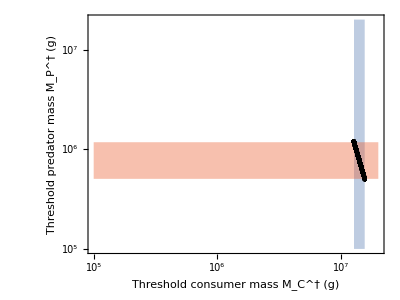

```mathematica
MegaMammalPlotGen=GraphicsRow[{
Show[{
ListDensityPlot[MaxConsumerSizePredPreyRatioSmall,PlotLegends->BarLegend[Automatic,LegendLabel->"M_C^† (g)"],FrameLabel->{"Prop. change PPMR χ_int","Prop. change PPMR χ_slope"}(*,RegionFunction->Function[{x,y,z},z>1.5*10^6&&z<1.74*10^7]*),ColorFunction->ColorData["AtlanticColors"],LabelStyle->Directive[FontSize->16],ScalingFunctions->{"Linear","Linear","Log"}],
ListPlot[Transpose[{MaxConsumerSizePredPreyRatio[[SizePlotPositions,1]],MaxConsumerSizePredPreyRatio[[SizePlotPositions,2]]}],Frame->True,PlotRange->{{-1,2},{-1,2}},AspectRatio->1,PlotStyle->Directive[White,Opacity[0.8]]](*,
Graphics[{Gray,Line[{0,-1},{0,2}]}],
Graphics[{Gray,Line[{-1,0},{2,0}]}]*)
},ImageSize->350],
Show[{
ListDensityPlot[MaxPredatorSizePredPreyRatioSmall,PlotLegends->BarLegend[Automatic,LegendLabel->"M_P^†(g)"],FrameLabel->{"Prop. change PPMR χ_int","Prop. change PPMR χ_slope"}(*,RegionFunction->Function[{x,y,z},z>500000&&z<1.2*10^6]*),ColorFunction->ColorData["SiennaTones"],LabelStyle->Directive[FontSize->16],ScalingFunctions->{"Linear","Linear","Log"}],
ListPlot[Transpose[{MaxConsumerSizePredPreyRatio[[SizePlotPositions,1]],MaxConsumerSizePredPreyRatio[[SizePlotPositions,2]]}],Frame->True,PlotRange->{{-1,2},{-1,2}},AspectRatio->1,PlotStyle->Directive[White,Opacity[0.8]]](*,
Graphics[{Gray,Line[{0,-1},{0,2}]}],
Graphics[{Gray,Line[{-1,0},{2,0}]}]*)
},ImageSize->350],
Show[{
ListLogLogPlot[Transpose[{MaxConsumerSizePredPreyRatio[[SizePlotPositions,3]],MaxPredatorSizePredPreyRatio[[SizePlotPositions,3]]}],PlotStyle->Black,Frame->True,PlotRange->{{1*10^5,2*10^7},{1*10^5,2*10^7}},FrameLabel->{"Threshold consumer mass M_C^† (g)","Threshold predator mass M_P^† (g)"},LabelStyle->Directive[FontSize->16]],
Graphics[{ColorData[97,1],Opacity[0.4],Rectangle[{Log@First[MaxConsumerSizePredPreyRatio[[SizePlotPositions,3]]],Log@(1*10^5)},{Log@Last[MaxConsumerSizePredPreyRatio[[SizePlotPositions,3]]],Log@(2*10^7)}]}],
Graphics[{ColorData[97,4],Opacity[0.4],Rectangle[{Log@(1*10^5),Log@First[MaxPredatorSizePredPreyRatio[[SizePlotPositions,3]]]},{Log@(2*10^7),Log@Last[MaxPredatorSizePredPreyRatio[[SizePlotPositions,3]]]}]}],
ListLogLogPlot[Transpose[{MaxConsumerSizePredPreyRatio[[SizePlotPositions,3]],MaxPredatorSizePredPreyRatio[[SizePlotPositions,3]]}],PlotStyle->{PointSize[Medium],Black}]
},ImageSize->400,AspectRatio->0.75]
},ImageSize->1350,Spacings->Scaled[-0.01]]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_megamammal_generalist.pdf"}],MegaMammalPlotGen,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2021_TaranWebs/figures/fig_megamammal_generalist.pdf

```mathematica
0.37-1
```

-0.63